# Christopher Greene Homework 4

## Problem 3.10

A damped harmonic oscillator with m = 10 kg, k = 250 N/m, and c = 60 kg/s is subject to a driving force given by F0 Cos ωt, where F0 = 48 N.  
a) What value of ω results in steady-state oscillations with maximum amplitude?

```mathematica
m = 10;
k = 250;
F0 = 48;
c = 60;
```

In order to find a value for ω, we need to first calculate the damping factor γ and frequency ω0

```mathematica
γ = c/(2m)
```

3

```mathematica
ω0 = Sqrt[k/m]
```

5

from there we can calculate the driving frequency ωd,

```mathematica
ω0^2-γ^2
```

16

```mathematica
ωd^2==ω0^2-γ^2
```

ωd^2==16

However, we also need the value for the response

```mathematica
ωr^2==16 - γ^2
```

ωr^2==7

```mathematica
ωr = Sqrt[7]
```

√7

B) From this initial condition, what is the maximum amplitude?
Maximum amplitude is calculated from Eq. 3.6.13a,

```mathematica
Amax = (F0/m)/(2γ Sqrt[ω0^2-γ^2])
```

1/5

```mathematica
N[Amax]
```

0.2

The maximum amplitude of this system is 0.2 m.
c) What is the phase shift? 
We find the phase shift from equation 3.6.8

```mathematica
Tan[ϕ] = (2γ ωr)/(ω0^2-ωr^2)
```

Set::write: Tag Tan in Tan[ϕ] is Protected.

(√7)/3

```mathematica
ϕ = ArcTan[(2γ ωr)/(ω0^2-ωr^2)]
```

ArcTan[(√7)/3]

```mathematica
N[ϕ]
```

0.722734

Converting to degrees.

```mathematica
ArcTan[(2γ ωr)/(ω0^2-ωr^2)]
```

ArcTan[(√7)/3]

```mathematica
With[{d=N[ArcTan[(√7)/3]/°]},Defer[d °]]
```

41.4096 °

There is a phase shift of 41.4 degrees for this system.

## Problem 3.16

If a series LCR circuit is connected across the terminals of an electric generator that produces a voltage V = V0 e^(iωt).  The flow of electrical energy q is given by the following equation:

L* (ⅆ^2 q)/(ⅆ t^2)+R*ⅆq/ⅆt+1/c q=V0 E^(i*ω*t)

a) Verify the correspondence shown in Table 3.6.1 between the parameter of a driven mechanical oscillator and the above driven electrical oscillator.

The equations for mechanical motion from Eq. 3.6.4,

m*(ⅆ^2 x)/(ⅆ t^2)+c*ⅆx/ⅆt+k*x=F0*E^(i*ω*t)

As we can see, mass acts as the analog for inductance, c, the damping resistance is the same as resistance, k is the reciprocal of capacitance, and F0 is the initial potential difference V0.

B) Calculate Q of the electric circuit in terms of the coefficients given above.

```mathematica
Q = ωd/(2γ)=Sqrt[ω0^2-γ^2]/(2γ)
```

```mathematica
ω0 = Sqrt[1/(L*c)];
γ = R/(2*L);
```

```mathematica
Q=Sqrt[ω0^2-γ^2]/(2γ)
```

(L √(1/(c L)-R^2/(4 L^2)))/R

C) Show that in the case of small damping, Q can be written as R0/R, where R0 = Sqrt[L/C] is the characteristic impedance of the circuit.

```mathematica
Q = ω0/(2γ)
```

(√(1/(c L)) L)/R

```mathematica
Simplify[Q]
```

(√(1/(c L)) L)/R

```mathematica
(1/(L*c))/(2(R/(2*L)))
```

1/(c R)

```mathematica
R0 = Sqrt[L/c]
```

√(L/c)

```mathematica
R0/R
```

(√(L/c))/R

Mathematica is weird and won’t cancel terms, but they are equal.

## C 3.1

The exact equation of motion for a simple pendulum of length L is given by

θ^(..)+ω0^2 Sin[θ]=0

where ω0^2=g/L.  Find θ(t) by integrating this equation of motion. Let L  = 1.00 m, θ0 = π/2, OverDot[θ0]=0

a) Plot θ(t)  from t =0 to t = 4 s.  Aso plot the solution for the small angle solution on the same graph.

```mathematica
g =9.8;
L = 1;
ω0 = Sqrt[g/L];
θ = π/2;
vθ = 0;
ti =0;
tf=4;
dt = 0.05;
```

π/2

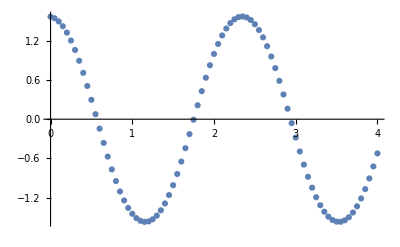

```mathematica
modeldata ={{ti,θ}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)

ax=-ω0^2*Sin[θ];
(* redefine y, vy, in terms of the values from the previous step *)

vθ = vθ+ ax dt;
θ= θ+ vθ dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,θ}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

The small angle approximation for a pendulum allows us to write Sinθ = θ

```mathematica
Clear[θ,t]
```

```mathematica
Clear[ω0]
```

```mathematica
DSolve[{x''[t]+ω0^2 x[t]==0,x[0]==π/2,x'[0]==0},x[t],t]
```

{{x[t]→1/2 π Cos[t ω0]}}

```mathematica
θ[t_]=π/2*Cos[ω0*t]
```

1/2 π Cos[t ω0]

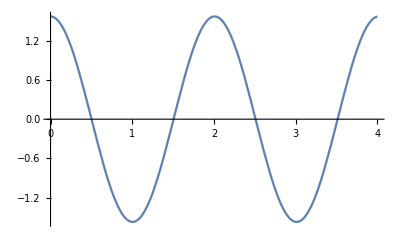

```mathematica
smallangle = Plot[1/2 π Cos[t ω0],{t,0,4}]
```

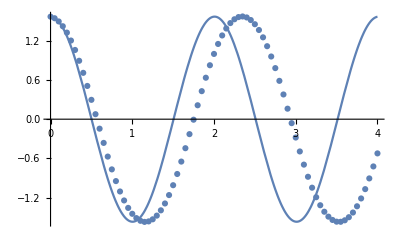

```mathematica
Show[{dataplot,smallangle}]
```

b) repeat a for θ0 = 3.10 rad

```mathematica
g =9.8;
L = 1;
ω0 = Sqrt[g/L];
θ = 3.10;
vθ = 0;
ti =0;
tf=4;
dt = 0.05;
```

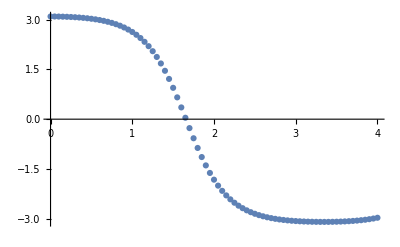

```mathematica
modeldata ={{ti,θ}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)

ax=-ω0^2*Sin[θ];
(* redefine y, vy, in terms of the values from the previous step *)

vθ = vθ+ ax dt;
θ= θ+ vθ dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,θ}];

];

dataplot = ListPlot[modeldata];
Show[{dataplot},PlotRange->All]
```

```mathematica
Clear[θ,t]
```

```mathematica
θ[t_]= 3.10*Cos[ω0*t]
```

3.1 Cos[3.1305 t]

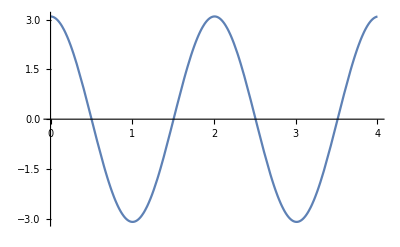

```mathematica
smallangle2 = Plot[3.1 Cos[3.1304951684997055 t],{t,0,4}]
```

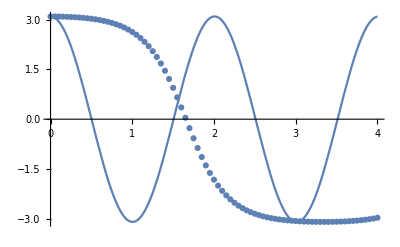

```mathematica
Show[{dataplot,smallangle2}]
```

c) Plot the period of the pendulum as a function of the amplitude θ0 from 0 to 3.10 rad. 
Looking on hyperphysics, they found that period as a function of amplitude is an elliptic integral that can be approximated by a series, with the first three terms being.

```mathematica
T[θ0_] =2π*ω0(1+1/16 θ0^2+11/3072 θ0^4)
```

19.6695 (1+θ0^2/16+(11 θ0^4)/3072)

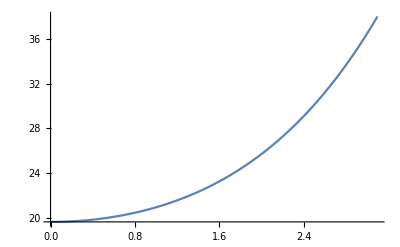

```mathematica
Plot[19.66948124691403 (1+θ0^2/16+(11 θ0^4)/3072),{θ0,0,3.10}]
```